```mathematica
Exact Solution Plots
```

```mathematica
y[x_]:=Sqrt[x]*(BesselJ[(1/6),(8/(3*eps))]*BesselJ[(-1/6),(x^3)/(3*eps)]-BesselJ[(-1/6),8/(3*eps)]*BesselJ[(1/6),(x^3)/(3*eps)])/(BesselJ[(-1/6),1/(3*eps)]*BesselJ[(1/6),8/(3*eps)]-BesselJ[-(1/6),(8/(3*eps))]*BesselJ[1/6,8/(3*eps)]);
```

```mathematica
y[x]
```

(√x (BesselJ[-1/6,x^3/(3 eps)] BesselJ[1/6,8/(3 eps)]-BesselJ[-1/6,8/(3 eps)] BesselJ[1/6,x^3/(3 eps)]))/(BesselJ[-1/6,1/(3 eps)] BesselJ[1/6,8/(3 eps)]-BesselJ[-1/6,8/(3 eps)] BesselJ[1/6,8/(3 eps)])

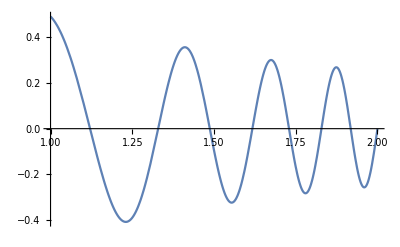

```mathematica
E1=Plot[y[x]/.{eps->0.1},{x,1,2}]
```

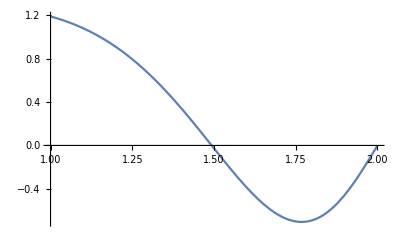

```mathematica
E2=Plot[y[x]/.{eps->0.5},{x,1,2}]
```

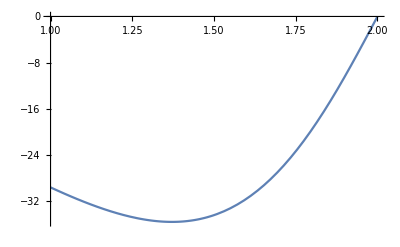

```mathematica
E3=Plot[y[x]/.{eps->1},{x,1,2}]
```

```mathematica
Algrebra for the Approximate Solution
```

```mathematica
apr[x_]:=A1*(x^-1)Exp[(eps^-1)*I*(x^3/3)]+A2*(x^-1)*Exp[-(eps^-1)*I*(x^3/3)]
```

```mathematica
apr[x_]:=-ⅇ^(-ⅈ/3/eps)/(-1+ⅇ^((14 ⅈ)/3/eps))*(x^-1)Exp[(eps^-1)*I*(x^3/3)]+ⅇ^(-ⅈ/3/eps)/(-1+ⅇ^((14 ⅈ)/3/eps))*ⅇ^((16 ⅈ)/3/eps)*(x^-1)*Exp[-(eps^-1)*I*(x^3/3)]
```

```mathematica
Simplify[apr[x]]
```

(ⅇ^(-(ⅈ (1+x^3))/(3 eps)) (ⅇ^((16 ⅈ)/3/eps)-ⅇ^((2 ⅈ x^3)/(3 eps))))/((-1+ⅇ^((14 ⅈ)/3/eps)) x)

```mathematica
ExpToTrig[apr[x]]
```

-Cos[1/(3 eps)-x^3/(3 eps)]/(x (-1+Cos[14/(3 eps)]+ⅈ Sin[14/(3 eps)]))+Cos[5/eps-x^3/(3 eps)]/(x (-1+Cos[14/(3 eps)]+ⅈ Sin[14/(3 eps)]))+(ⅈ Sin[1/(3 eps)-x^3/(3 eps)])/(x (-1+Cos[14/(3 eps)]+ⅈ Sin[14/(3 eps)]))+(ⅈ Sin[5/eps-x^3/(3 eps)])/(x (-1+Cos[14/(3 eps)]+ⅈ Sin[14/(3 eps)]))

```mathematica
Simplify[%31]
```

-(Csc[7/(3 eps)] Sin[(-8+x^3)/(3 eps)])/x

```mathematica
Approximate Solution Plots
```

```mathematica
apr[x_]:=-(Csc[7/(3 eps)] Sin[(-8+x^3)/(3 eps)])/x;
```

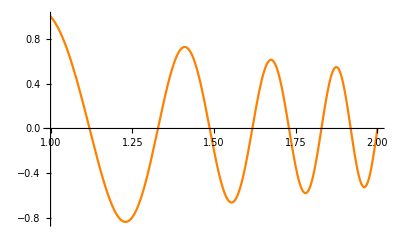

```mathematica
A1=Plot[apr[x]/.{eps->0.1},{x,1,2},PlotStyle->Orange]
```

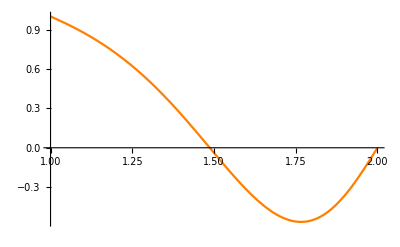

```mathematica
A2=Plot[apr[x]/.{eps->0.5},{x,1,2},PlotStyle->Orange]
```

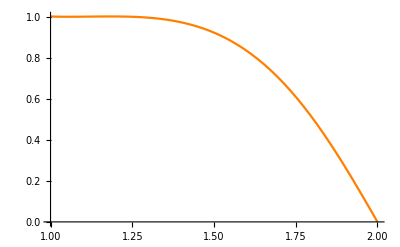

```mathematica
A3=Plot[apr[x]/.{eps->1},{x,1,2},PlotStyle->Orange]
```

```mathematica
Comparison
```

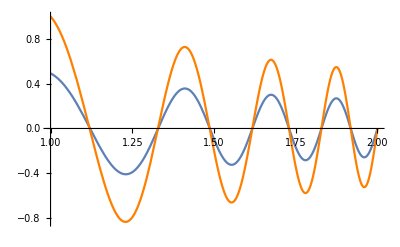

```mathematica
Show[E1,A1,PlotRange->All]
```

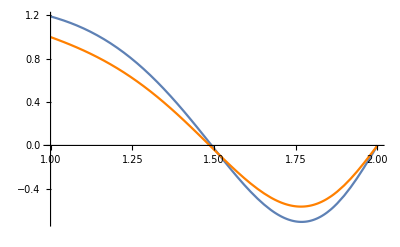

```mathematica
Show[E2,A2,PlotRange->All]
```

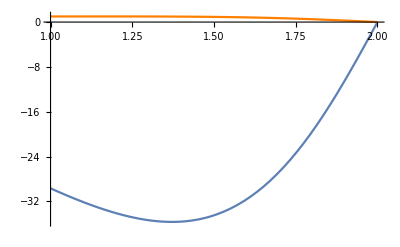

```mathematica
Show[E3,A3,PlotRange->All]
```